Carbapenem Resistance Model:

Objective: Whereas a clear correlation exists between consumption of antibiotics and the evolution of resistance in microbial communities, the effect of reduction of usage is less clear. To project the future frequency of carbapenem resistance, based on yearly surveillance data and consumption data. A population genetic model was adapted to retrospectively estimate the relationship between evolutionary fitness of carbapenem resistance and carbapenem consumption.

Derivation: We fit the historical selection to consumption via a deterministic, continuous-time haploid model of the frequency of resistance. See, for reference: 1) Hartl, Daniel L., Andrew G. Clark, and Andrew G. Clark. Principles of population genetics. Vol. 116. Sunderland: Sinauer associates, 1997—base population genetic model; 2) Nielsen, K. M., & Townsend, J. P. (2004). Monitoring and modeling horizontal gene transfer. Nature biotechnology, 22(9), 1110-1114—relation of base model to novel DNA such as antimicrobial resistance elements; and 3) Johnsen, P. J., Townsend, J. P., Bøhn, T., Simonsen, G. S., Sundsfjord, A., & Nielsen, K. M. (2011). Retrospective evidence for a biological cost of vancomycin resistance determinants in the absence of glycopeptide selective pressures. Journal of antimicrobial chemotherapy, 66(3), 608-610 —application of base model to project future vancomycin resistance after ban of use.

```mathematica
ClearAll["Global`*"]
```

```mathematica
r[t_,p0_,a_]:=ⅇ^(a*c[[t]]* t)/((1/p0)-1+ⅇ^(a *c[[t]]*t)) ;
```

Where r is the frequency of resistance at time t, p0 is the initial frequency of resistance, and a is the continuous time Malthusian selection coefficient

Below, we apply this model in a preliminary case to the United States.

```mathematica
Note that the likelihood function used here will additionally be improved from that used in the preliminary model above. Because surveillance is conducted by sampling and testing for resistance, likelihood can be quantified under better distributional assumptions, with greater accuracy and precision. Instead of the observed frequencies of resistance (which are not certain), likelihood can be calculated based on the observed cases of resistant (UKResistance, above) vs. non-resistant (UKIsolates – UKResistance, above) measured by surveillance—see for instance, Johnsen, P. J., Townsend, J. P., Bøhn, T., Simonsen, G. S., Sundsfjord, A., & Nielsen, K. M. (2011). Retrospective evidence for a biological cost of vancomycin resistance determinants in the absence of glycopeptide selective pressures. Journal of antimicrobial chemotherapy, 66(3), 608-610.
```

```mathematica
Load Data
```

Number of resistant isolates recovered, each year 2005–2014; Number of isolates tested, each year 2005–2014, estimated frequencies of resistance, 2005–2014.

```mathematica
SetDirectory[NotebookDirectory[]];
CountryName="United States";
Data=Import["DataSheet.xlsx",{"Data",CountryName}];
c=Drop[Data[[2]],1];
Isolates=Drop[Data[[3]],1];
Resistance=Drop[Data[[4]],1];
RData=Resistance/Isolates;
```

```mathematica
Maximum Likelihood Function
```

Likelihood function and plot: values for p0 are plotted along the x-axis (bottom), likelihood is quantified along the z-axis (left side), and amount of selection imposed per unit of consumption is plotted along the y-axis (top).

```mathematica
LikUK[p0_,a_]:= Total[Table[Log[Binomial[Isolates[[j]],Resistance[[j]]]]+Resistance[[j]]*Log[r[j-1,p0,a]]+(Isolates[[j]]-Resistance[[j]])*Log[1-r[j-1,p0,a]],{j,1,13}]]
```

```mathematica
LikUK[0.001,2]
```

Indeterminate

```mathematica
Plot3D[LikUK[p0,a],{p0,0,1},{a,-10,10},PlotLabel-> UnitedStates, AxesLabel->{p0, a,Likelihood}]
(*Note that the bounds for p0 must be less than 1*)
```

-Graphics3D-

```mathematica
{max,{fittedp0,fitteda}}=FindMaximum[{LikUK[p0,a],0.005≤ p0≤ 1,a≤0},{p0,a}]
```

{-790.428,{p0→0.0212836,a→-3.8554×10^-13}}

Plot over time

```mathematica
Years=Range[2000,2012];
Res=Transpose@{Years,RData};
t=Range[1,13];
```

```mathematica
ModelFit=Transpose@{Years,r[t,fittedp0[[2]],fitteda[[2]]]}
```

{{2000,0.0212836},{2001,0.0212836},{2002,0.0212836},{2003,0.0212836},{2004,0.0212836},{2005,0.0212836},{2006,0.0212836},{2007,0.0212836},{2008,0.0212836},{2009,0.0212836},{2010,0.0212836},{2011,0.0212836},{2012,0.0212836}}

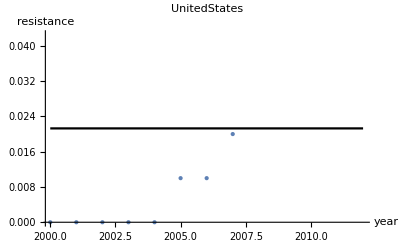

```mathematica
plot1=ListLinePlot[ModelFit, PlotStyle-> {Black},AxesLabel->{year,resistance},PlotLabel-> UnitedStates, PlotRange-> All];
plot2=ListPlot[{Res}, PlotStyle-> PointSize[Large],PlotRange-> All];
Show[plot1,plot2]
```

```mathematica
Least Squares (Preliminary)
```

```mathematica
Lik[t_,p0_,a_]:=(r[t,p0,a]-RData[[t]])^2;
(* Calculate the sum of the square difference between model output and resistance data (Rdata) then minimize the likelihood to find parameters a and p0 *)
```

```mathematica
t=Range[1,10];
```

```mathematica
Liksum[p0_,a_]:=Total[Lik[t,p0,a]];
```

```mathematica
{max,{LSp0,LSa}}=FindMinimum[{Liksum[p0,a],.005≤ p0≤1},{p0,a}]
```

{0.00010638,{p0→0.0052222,a→6.47346}}

```mathematica
LSModelFit=Transpose@{Years,r[t,LSp0[[2]],LSa[[2]]]};
```

Graphical demonstration of the minimum (least squares):

```mathematica
Plot3D[Liksum[p0,a],{p0,0.004,0.0065},{a,3,10}]
```

-Graphics3D-

Values for p0 are plotted along the x-axis (bottom), likelihood is quantified along the z-axis (left side), and amount of selection imposed per unit of consumption is plotted along the y-axis (top).

The coefficient conveying the amount of selection imposed per unit of consumption (here, a = 6.5) can then be used in our evoutionary model to project future carbapenem resistance in response to any future scenario of carbapenem consumption. With future levels of carbapenem resistance in a given scenario in hand, we can apply methods of cost-effectiveness in the face of future discounting to quantify appropriate policies of carbapenem sparing.

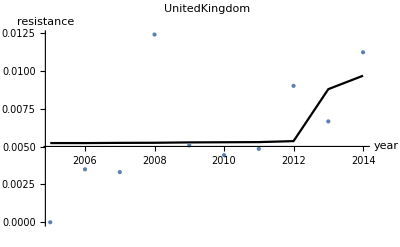

```mathematica
plot1=ListLinePlot[LSModelFit, PlotStyle-> {Black},AxesLabel->{year,resistance},PlotLabel-> UnitedKingdom, PlotRange-> All];
plot2=ListPlot[{Res}, PlotStyle-> PointSize[Large],PlotRange-> All];
Show[plot1,plot2,PlotRange-> All]
```